```mathematica
Spectrum[g_Graph]:=Sort[Tally@Eigenvalues@AdjacencyMatrix[g],NumericalOrder];
Spectrum[m_]:=Sort[Tally@Eigenvalues[m],NumericalOrder];
```

```mathematica
G[sigma_Integer,k_Integer,opts___]:=Graph[Join[
Flatten[Table[{i,u}<->{i,v},{i,2sigma-1},{u,2sigma-1,k},{v,u+1,k+1}],2],
Flatten[Table[{{i,u}<->{i,v},{i,u+1}<->{i,v}},{i,2sigma-1},{u,1,2sigma-3,2},{v,u+2,k+1}],3],
Flatten[Table[{i,2j}<->{Mod[i+j,2sigma-1,1],2j-1},{i,2sigma-1},{j,sigma-1}],1]
],opts]
```

```mathematica
QuotientAdjacencyMatrix[g_Graph,s_List]:=SparseArray@Flatten[If[#1==#2,{#1,#2}->(2#3)/Length[s⟦#1⟧],{{#1,#2}->#3/Length[s⟦#1⟧],{#2,#1}->#3/Length[s⟦#2⟧]}]&@@@({First[#1],Last[#1],#2}&@@@Tally[EdgeList[g]/.Flatten[Thread/@MapIndexed[Rule[#1,First[#2]]&,s],1]]),1]
```

```mathematica
f[sigma_]:=f[sigma]={Collect[#1,{x,k}],#2}&@@@FactorList@CharacteristicPolynomial[Normal@QuotientAdjacencyMatrix[G[sigma,2sigma],Join[Table[{i,j},{i,2sigma-1},{j,2sigma-1,2sigma+1}],List/@Flatten[Table[{i,j},{i,2sigma-1},{j,2sigma-2}],1]]]/.{2->k-2sigma+2,3->k-2sigma+3},x]
```

### Small Examples

Graph W_4 for σ = 2.

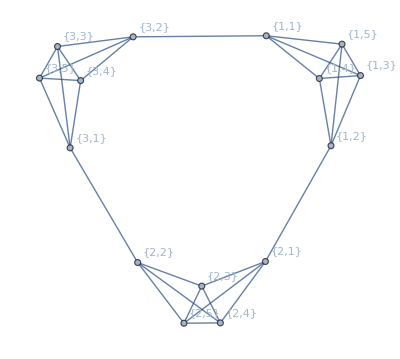

```mathematica
G[2,4,VertexLabels->Automatic]
```

Spectrum and Characteristic Polynomial of Quotient Matrix

```mathematica
Spectrum[%]
```

{{Root-2.20Root[5-7 #1-2 #1^2+#1^3&,1]-2.2044015503294316,2},{-1,8},{Root0.636Root[5-7 #1-2 #1^2+#1^3&,2]0.6355519407979247,2},{Root3.57Root[5-7 #1-2 #1^2+#1^3&,3]3.5688496095315068,2},{4,1}}

```mathematica
f[2]
```

{{1,1},{k-x,1},{1+x,2},{3-2 k+(-1+2 k) x+(-2+k) x^2-x^3,2}}

Vertex Partition and Quotient Matrix of W_4.

```mathematica
Join[Table[{i,j},{i,3},{j,3,5}],List/@Flatten[Table[{i,j},{i,3},{j,2}],1]]
```

{{{1,3},{1,4},{1,5}},{{2,3},{2,4},{2,5}},{{3,3},{3,4},{3,5}},{{1,1}},{{1,2}},{{2,1}},{{2,2}},{{3,1}},{{3,2}}}

```mathematica
Normal@QuotientAdjacencyMatrix[G[2,4],%]/.{2->k-2,3->k-1}//MatrixForm
```

(-2+k | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | -2+k | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | -2+k | 0 | 0 | 0 | 0 | 1 | 1
-1+k | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1+k | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | -1+k | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | -1+k | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | -1+k | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | -1+k | 1 | 0 | 0 | 0 | 0 | 0)

Z_10 for σ = 3.

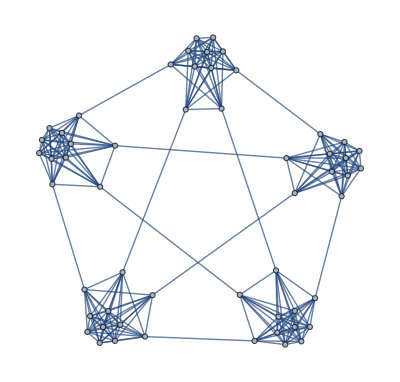

```mathematica
G[3,10]
```

```mathematica
Spectrum[%]
```

{{Root-2.67Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,1]-2.673406618914421,4},{Root-1.94Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,2]-1.9371580400262038,4},{-1,34},{Root0.113Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,3]0.11282166160568745,4},{Root0.891Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,4]0.8907593482328576,4},{Root9.61Root[-5+46 #1-11 #1^2-34 #1^3-6 #1^4+#1^5&,5]9.60698364910208,4},{10,1}}

```mathematica
f[3]
```

{{1,1},{k-x,1},{1+x,4},{-5+k+(14-6 k) x+(1+k) x^2+(-6+4 k) x^3+(-4+k) x^4-x^5,4}}

A_8 for σ = 4.

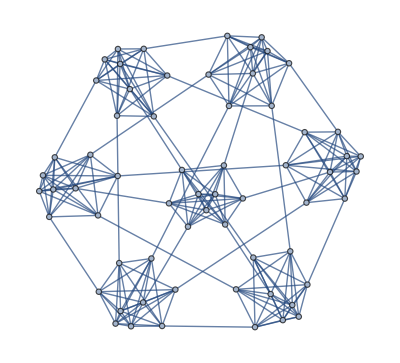

```mathematica
G[4,8]
```

```mathematica
Spectrum[%]
```

{{Root-2.79Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.790292237102982,6},{Root-2.22Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-2.219894418526786,6},{Root-1.52Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.5230990939427331,6},{-1,20},{Root-0.244Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.24413307321199104,6},{Root0.503Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.502880455004431,6},{Root0.942Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9419581784639768,6},{Root7.33Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.332580189316085,6},{8,1}}

```mathematica
f[4]
```

{{1,1},{k-x,1},{1+x,6},{k+(-29+6 k) x+(36-13 k) x^2+(27-8 k) x^3+(-13+8 k) x^4+(-15+6 k) x^5+(-6+k) x^6-x^7,6}}

Check second eigenvalue for higher σ.

```mathematica
Apply[And,Table[Reduce[f[s,x]==0&&k-(2s-1)/(k+1)≤x<k]=!=False,{s,2,6},{k,2s,1000}],{0,1}]
```

True

### Testing

```mathematica
Table[GraphAutomorphismGroup@G[s,2s],{s,2,7}]
```

{PermutationGroup[{Cycles[{{2,3}}],Cycles[{{5,6}}],Cycles[{{8,9}}],Cycles[{{7,8}}],Cycles[{{4,5}}],Cycles[{{4,7},{5,8},{6,9},{10,11},{12,15},{13,14}}],Cycles[{{1,2}}],Cycles[{{1,4},{2,5},{3,6},{10,13},{11,12},{14,15}}]}],PermutationGroup[{Cycles[{{5,6}}],Cycles[{{8,9}}],Cycles[{{7,8}}],Cycles[{{11,12}}],Cycles[{{10,11}}],Cycles[{{14,15}}],Cycles[{{13,14}}],Cycles[{{2,3}}],Cycles[{{4,5}}],Cycles[{{4,7,13,10},{5,8,14,11},{6,9,15,12},{16,17,18,19},{20,25,34,31},{21,26,35,28},{22,27,32,29},{23,24,33,30}}],Cycles[{{1,2}}],Cycles[{{1,4},{2,5},{3,6},{7,13},{8,14},{9,15},{16,22},{17,23},{18,20},{19,21},{24,34},{25,35},{26,32},{27,33},{28,30},{29,31}}]}],PermutationGroup[{Cycles[{{5,6}}],Cycles[{{8,9}}],Cycles[{{7,8}}],Cycles[{{20,21}}],Cycles[{{19,20}}],Cycles[{{14,15}}],Cycles[{{13,14}}],Cycles[{{17,18}}],Cycles[{{16,17}}],Cycles[{{11,12}}],Cycles[{{10,11}}],Cycles[{{2,3}}],Cycles[{{4,5}}],Cycles[{{4,7,13},{5,8,14},{6,9,15},{10,19,16},{11,20,17},{12,21,18},{22,23,27},{24,25,26},{28,35,51},{29,39,46},{30,37,50},{31,38,48},{32,36,49},{33,34,47},{40,59,57},{41,63,52},{42,61,56},{43,62,54},{44,60,55},{45,58,53}}],Cycles[{{4,10,7,19,13,16},{5,11,8,20,14,17},{6,12,9,21,15,18},{22,26,23,24,27,25},{28,44,35,60,51,55},{29,42,39,61,46,56},{30,45,37,58,50,53},{31,40,38,59,48,57},{32,41,36,63,49,52},{33,43,34,62,47,54}}],Cycles[{{1,2}}],Cycles[{{1,4},{2,5},{3,6},{7,19},{8,20},{9,21},{10,16},{11,17},{12,18},{22,30},{23,31},{24,28},{25,29},{26,33},{27,32},{34,60},{35,61},{36,58},{37,59},{38,63},{39,62},{40,54},{41,55},{42,52},{43,53},{44,57},{45,56},{46,48},{47,49},{50,51}}]}],PermutationGroup[{Cycles[{{20,21}}],Cycles[{{19,20}}],Cycles[{{11,12}}],Cycles[{{10,11}}],Cycles[{{5,6}}],Cycles[{{8,9}}],Cycles[{{7,8}}],Cycles[{{26,27}}],Cycles[{{25,26}}],Cycles[{{14,15}}],Cycles[{{13,14}}],Cycles[{{17,18}}],Cycles[{{16,17}}],Cycles[{{23,24}}],Cycles[{{22,23}}],Cycles[{{2,3}}],Cycles[{{4,5}}],Cycles[{{4,7,13,25,22,16},{5,8,14,26,23,17},{6,9,15,27,24,18},{10,19},{11,20},{12,21},{28,29,34,30,31,35},{32,33},{36,45,66,94,87,75},{37,50,62,95,91,68},{38,47,67,92,85,74},{39,51,60,93,90,70},{40,49,64,97,88,73},{41,48,65,96,89,72},{42,46,63,99,84,69},{43,44,61,98,86,71},{52,77,58,78,55,83},{53,82,54,79,59,76},{56,81},{57,80}}],Cycles[{{1,2}}],Cycles[{{1,4},{2,5},{3,6},{7,25},{8,26},{9,27},{10,22},{11,23},{12,24},{13,19},{14,20},{15,21},{28,38},{29,39},{30,36},{31,37},{32,41},{33,40},{34,43},{35,42},{44,94},{45,95},{46,92},{47,93},{48,97},{49,96},{50,99},{51,98},{52,86},{53,87},{54,84},{55,85},{56,89},{57,88},{58,91},{59,90},{60,78},{61,79},{62,76},{63,77},{64,81},{65,80},{66,83},{67,82},{68,70},{69,71},{72,73},{74,75}}]}],PermutationGroup[{Cycles[{{5,6}}],Cycles[{{8,9}}],Cycles[{{7,8}}],Cycles[{{32,33}}],Cycles[{{31,32}}],Cycles[{{14,15}}],Cycles[{{13,14}}],Cycles[{{26,27}}],Cycles[{{25,26}}],Cycles[{{23,24}}],Cycles[{{22,23}}],Cycles[{{17,18}}],Cycles[{{16,17}}],Cycles[{{20,21}}],Cycles[{{19,20}}],Cycles[{{29,30}}],Cycles[{{28,29}}],Cycles[{{11,12}}],Cycles[{{10,11}}],Cycles[{{2,3}}],Cycles[{{4,5}}],Cycles[{{4,7,13,25,16,31,28,22,10,19},{5,8,14,26,17,32,29,23,11,20},{6,9,15,27,18,33,30,24,12,21},{34,35,40,39,42,36,37,41,38,43},{44,55,80,119,92,136,127,111,68,103},{45,60,79,122,86,137,131,108,73,94},{46,57,81,118,93,134,125,110,69,102},{47,61,78,123,84,135,130,109,72,96},{48,63,74,115,90,139,132,106,67,101},{49,62,76,117,91,138,133,104,65,100},{50,59,82,116,87,141,128,113,64,95},{51,58,83,114,85,140,129,112,66,97},{52,56,77,121,88,143,124,105,70,99},{53,54,75,120,89,142,126,107,71,98}}],Cycles[{{1,2}}],Cycles[{{1,4},{2,5},{3,6},{7,31},{8,32},{9,33},{10,28},{11,29},{12,30},{13,25},{14,26},{15,27},{16,22},{17,23},{18,24},{34,46},{35,47},{36,44},{37,45},{38,49},{39,48},{40,51},{41,50},{42,53},{43,52},{54,136},{55,137},{56,134},{57,135},{58,139},{59,138},{60,141},{61,140},{62,143},{63,142},{64,126},{65,127},{66,124},{67,125},{68,129},{69,128},{70,131},{71,130},{72,133},{73,132},{74,116},{75,117},{76,114},{77,115},{78,119},{79,118},{80,121},{81,120},{82,123},{83,122},{84,106},{85,107},{86,104},{87,105},{88,109},{89,108},{90,111},{91,110},{92,113},{93,112},{94,96},{95,97},{98,99},{100,101},{102,103}}]}],PermutationGroup[{Cycles[{{5,6}}],Cycles[{{8,9}}],Cycles[{{7,8}}],Cycles[{{38,39}}],Cycles[{{37,38}}],Cycles[{{14,15}}],Cycles[{{13,14}}],Cycles[{{26,27}}],Cycles[{{25,26}}],Cycles[{{11,12}}],Cycles[{{10,11}}],Cycles[{{20,21}}],Cycles[{{19,20}}],Cycles[{{35,36}}],Cycles[{{34,35}}],Cycles[{{29,30}}],Cycles[{{28,29}}],Cycles[{{32,33}}],Cycles[{{31,32}}],Cycles[{{17,18}}],Cycles[{{16,17}}],Cycles[{{23,24}}],Cycles[{{22,23}}],Cycles[{{2,3}}],Cycles[{{4,5}}],Cycles[{{4,7,13,25,10,19,37,34,28,16,31,22},{5,8,14,26,11,20,38,35,29,17,32,23},{6,9,15,27,12,21,39,36,30,18,33,24},{40,41,46,49,44,50,42,43,47,48,45,51},{52,65,94,145,80,122,186,175,155,108,165,135},{53,70,97,140,86,114,187,179,156,105,171,124},{54,67,95,144,81,123,184,173,154,109,164,134},{55,71,96,141,87,112,185,178,157,104,170,126},{56,74,90,139,83,120,189,183,148,101,166,133},{57,75,88,137,82,121,188,182,150,103,167,132},{58,73,92,146,78,115,191,180,153,111,160,125},{59,72,93,147,76,113,190,181,152,110,162,127},{60,69,99,136,77,118,193,176,158,102,163,131},{61,68,98,138,79,119,192,177,159,100,161,130},{62,66,91,143,84,117,195,172,149,106,169,128},{63,64,89,142,85,116,194,174,151,107,168,129}}],Cycles[{{1,2}}],Cycles[{{1,4},{2,5},{3,6},{7,37},{8,38},{9,39},{10,34},{11,35},{12,36},{13,31},{14,32},{15,33},{16,28},{17,29},{18,30},{19,25},{20,26},{21,27},{40,54},{41,55},{42,52},{43,53},{44,57},{45,56},{46,59},{47,58},{48,61},{49,60},{50,63},{51,62},{64,186},{65,187},{66,184},{67,185},{68,189},{69,188},{70,191},{71,190},{72,193},{73,192},{74,195},{75,194},{76,174},{77,175},{78,172},{79,173},{80,177},{81,176},{82,179},{83,178},{84,181},{85,180},{86,183},{87,182},{88,162},{89,163},{90,160},{91,161},{92,165},{93,164},{94,167},{95,166},{96,169},{97,168},{98,171},{99,170},{100,150},{101,151},{102,148},{103,149},{104,153},{105,152},{106,155},{107,154},{108,157},{109,156},{110,159},{111,158},{112,138},{113,139},{114,136},{115,137},{116,141},{117,140},{118,143},{119,142},{120,145},{121,144},{122,147},{123,146},{124,126},{125,127},{128,129},{130,131},{132,133},{134,135}}]}]}

```mathematica
GroupOrder/@%5
```

{1296,155520,11757312,544195584,39907676160,2037468266496}

```mathematica
GroupOrder/@Table[GraphAutomorphismGroup@G[2,k],{k,4,7}]
```

{1296,82944,10368000,2239488000}

```mathematica
Table[f[s],{s,2,6}]
```

{{{1,1},{k-x,1},{1+x,2},{3-2 k+(-1+2 k) x+(-2+k) x^2-x^3,2}},{{1,1},{k-x,1},{1+x,4},{-5+k+(14-6 k) x+(1+k) x^2+(-6+4 k) x^3+(-4+k) x^4-x^5,4}},{{1,1},{k-x,1},{1+x,6},{k+(-29+6 k) x+(36-13 k) x^2+(27-8 k) x^3+(-13+8 k) x^4+(-15+6 k) x^5+(-6+k) x^6-x^7,6}},{{1,1},{k-x,1},{1+x,12},{-2+2 x+x^2,4},{9-2 k+(-7+2 k) x+(-2+k) x^2-x^3,2},{9-2 k+(11+2 k) x+(-119+25 k) x^2+(38-16 k) x^3+(133-38 k) x^4+(11+2 k) x^5+(-47+19 k) x^6+(-28+8 k) x^7+(-8+k) x^8-x^9,6}},{{1,1},{k-x,1},{1+x,10},{-11+k+(54-12 k) x+(122-10 k) x^2+(-364+76 k) x^3+(-175+23 k) x^4+(384-100 k) x^5+(232-54 k) x^6+(-78+32 k) x^7+(-109+34 k) x^8+(-45+10 k) x^9+(-10+k) x^10-x^11,10}}}

```mathematica
f[2,x_]:=3-2 k+(-1+2 k) x+(-2+k) x^2-x^3;
f[3,x_]:=-5+k+(14-6 k) x+(1+k) x^2+(-6+4 k) x^3+(-4+k) x^4-x^5;
f[4,x_]:=k+(-29+6 k) x+(36-13 k) x^2+(27-8 k) x^3+(-13+8 k) x^4+(-15+6 k) x^5+(-6+k) x^6-x^7
f[5,x_]:=(-2+2 x+x^2)(9-2 k+(-7+2 k) x+(-2+k) x^2-x^3)(9-2 k+(11+2 k) x+(-119+25 k) x^2+(38-16 k) x^3+(133-38 k) x^4+(11+2 k) x^5+(-47+19 k) x^6+(-28+8 k) x^7+(-8+k) x^8-x^9);
f[6,x_]:=-11+k+(54-12 k) x+(122-10 k) x^2+(-364+76 k) x^3+(-175+23 k) x^4+(384-100 k) x^5+(232-54 k) x^6+(-78+32 k) x^7+(-109+34 k) x^8+(-45+10 k) x^9+(-10+k) x^10-x^11
```

```mathematica
Table[Factor@f[s,1],{s,2,6}]
```

{-1+k,-1+k,-1+k,(-1+k)^2,-1+k}

```mathematica
Table[Factor@f[s,-1],{s,2,6}]
```

{-3 (-1+k),5 (-3+k),-7 (-5+k),81 (-7+k) (-5+k),-11 (-9+k)}

```mathematica
PolynomialQuotientRemainder[f[3,x],f[2,x],x]
```

{1+2 x+x^2,-8+3 k+(9-4 k) x+(2-2 k) x^2}

```mathematica
PolynomialQuotientRemainder[f[4,x],f[3,x],x]
```

{1+2 x+x^2,5+(-33+10 k) x+(12-3 k) x^2+(17-8 k) x^3+(2-2 k) x^4}

```mathematica
Table[Reduce[f[s,k-(2s-1)/(k+1)]>0&&k≥2s],{s,2,6}]
```

{k≥4,k≥6,k≥8,k≥10,k≥12}

```mathematica
lb[s_,k_]:=k-(2s-1)/(k+1)
```

Try new vertex partitioning

```mathematica
ClearAll[p]
```

```mathematica
p[sigma_,k_]:=p[sigma,k]=QuotientAdjacencyMatrix[G[sigma,k],Join[Table[{i,j},{i,2sigma-1},{j,2sigma-1,k+1}],Table[{i,j},{i,2sigma-1},{j,2sigma-2}]]]
```

```mathematica
Apply[And,Table[k-(2s-1)/(k+1)≤RankedMax[Eigenvalues@p[s,k],2],{s,2,6},{k,2s,50}],{0,1}]
```

True

```mathematica
p[2,4]//MatrixForm
```

(2 | 0 | 0 | 2 | 0 | 0
0 | 2 | 0 | 0 | 2 | 0
0 | 0 | 2 | 0 | 0 | 2
3 | 0 | 0 | 0 | 1/2 | 1/2
0 | 3 | 0 | 1/2 | 0 | 1/2
0 | 0 | 3 | 1/2 | 1/2 | 0)

```mathematica
p[3,9]//MatrixForm
```

(5 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0
0 | 5 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0
0 | 0 | 5 | 0 | 0 | 0 | 0 | 4 | 0 | 0
0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 4
6 | 0 | 0 | 0 | 0 | 2 | 1/4 | 1/4 | 1/4 | 1/4
0 | 6 | 0 | 0 | 0 | 1/4 | 2 | 1/4 | 1/4 | 1/4
0 | 0 | 6 | 0 | 0 | 1/4 | 1/4 | 2 | 1/4 | 1/4
0 | 0 | 0 | 6 | 0 | 1/4 | 1/4 | 1/4 | 2 | 1/4
0 | 0 | 0 | 0 | 6 | 1/4 | 1/4 | 1/4 | 1/4 | 2)

```mathematica
ClearAll[p]
```

```mathematica
p[s_,k_]:=p[s,k]=Simplify@Det[((k-2s+2-x)IdentityMatrix[2s-1]).((1/(2s-2))(1-IdentityMatrix[2s-1])+(2s-4-x)IdentityMatrix[2s-1])-(k-2s+3)(2s-2)IdentityMatrix[2s-1]]
```

```mathematica
p[3,9]
```

1/256 (61+27 x-4 x^2)^4 (-9-8 x+x^2)

```mathematica
p[6,100]
```

((1990+979 x-10 x^2)^10 (-100-99 x+x^2))/10000000000

```mathematica
Solve[%154==0,x]
```

{{x→-1},{x→100},{x→1/20 (979-√1038041)},{x→1/20 (979-√1038041)},{x→1/20 (979-√1038041)},{x→1/20 (979-√1038041)},{x→1/20 (979-√1038041)},{x→1/20 (979-√1038041)},{x→1/20 (979-√1038041)},{x→1/20 (979-√1038041)},{x→1/20 (979-√1038041)},{x→1/20 (979-√1038041)},{x→1/20 (979+√1038041)},{x→1/20 (979+√1038041)},{x→1/20 (979+√1038041)},{x→1/20 (979+√1038041)},{x→1/20 (979+√1038041)},{x→1/20 (979+√1038041)},{x→1/20 (979+√1038041)},{x→1/20 (979+√1038041)},{x→1/20 (979+√1038041)},{x→1/20 (979+√1038041)}}

```mathematica
DeleteDuplicates[%]
```

{{x→-1},{x→100},{x→1/20 (979-√1038041)},{x→1/20 (979+√1038041)}}

```mathematica
%//N
```

{{x→-1.},{x→100.},{x→-1.99215},{x→99.8921}}

```mathematica
Solve[l^2-(k-2)l+2m-2k-1+(l-k)/(2m-2)==0,l]
```

{{l→1/2 (-2+k+1/(2-2 m)-√((2-k-1/(2-2 m))^2-4 (-1-2 k+k/(2-2 m)+2 m)))},{l→1/2 (-2+k+1/(2-2 m)+√((2-k-1/(2-2 m))^2-4 (-1-2 k+k/(2-2 m)+2 m)))}}

```mathematica
l/.%183//TeXForm
```

\left\{\frac{1}{2} \left(-\sqrt{\left(-k-\frac{1}{2-2 m}+2\right)^2-4 \left(\frac{k}{2-2 m}-2 k+2 m-1\right)}+k+\frac{1}{2-2 m}-2\right),\frac{1}{2}
   \left(\sqrt{\left(-k-\frac{1}{2-2 m}+2\right)^2-4 \left(\frac{k}{2-2 m}-2 k+2 m-1\right)}+k+\frac{1}{2-2 m}-2\right)\right\}

```mathematica
Reduce[1/2 (-2+k+1/(2-2 m)+√((2-k-1/(2-2 m))^2-4 (-1-2 k+k/(2-2 m)+2 m)))≥k-(2m-1)/(k+1)&&k/2≥m≥2]
```

(k==4&&m==2)||(k>4&&2≤m≤k/2)

### More Testing

```mathematica
G[2,4]
```

{{1,3}<->{1,4},{1,3}<->{1,5},{1,4}<->{1,5},{2,3}<->{2,4},{2,3}<->{2,5},{2,4}<->{2,5},{3,3}<->{3,4},{3,3}<->{3,5},{3,4}<->{3,5},{1,1}<->{1,3},{1,2}<->{1,3},{1,1}<->{1,4},{1,2}<->{1,4},{1,1}<->{1,5},{1,2}<->{1,5},{2,1}<->{2,3},{2,2}<->{2,3},{2,1}<->{2,4},{2,2}<->{2,4},{2,1}<->{2,5},{2,2}<->{2,5},{3,1}<->{3,3},{3,2}<->{3,3},{3,1}<->{3,4},{3,2}<->{3,4},{3,1}<->{3,5},{3,2}<->{3,5}}

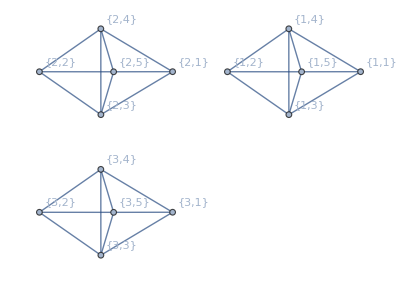

```mathematica
g=Graph[G[2,4],VertexLabels->Automatic]
```

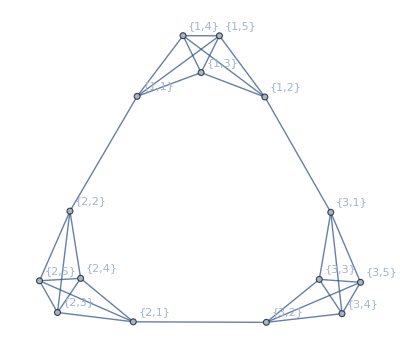

```mathematica
EdgeAdd[g,{{1,1}<->{2,2},{2,1}<->{3,2},{3,1}<->{1,2}}]
```

```mathematica
Spectrum[%30]
```

{{Root-2.20Root[5-7 #1-2 #1^2+#1^3&,1]-2.2044015503294316,2},{-1,8},{Root0.636Root[5-7 #1-2 #1^2+#1^3&,2]0.6355519407979247,2},{Root3.57Root[5-7 #1-2 #1^2+#1^3&,3]3.5688496095315068,2},{4,1}}

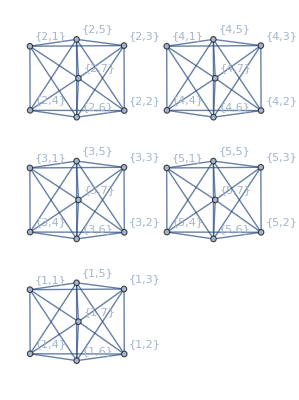

```mathematica
g=Graph[G[3,6],VertexLabels->Automatic]
```

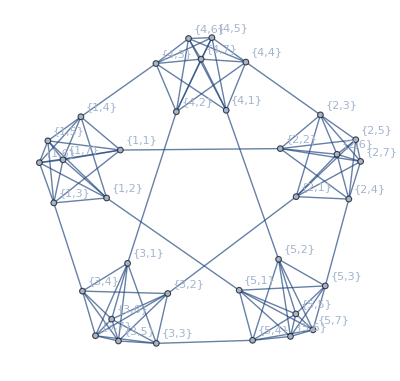

```mathematica
EdgeAdd[g,{{1,1}<->{2,2},{2,1}<->{3,2},{3,1}<->{4,2},{4,1}<->{5,2},{5,1}<->{1,2},
{1,3}<->{3,4},{3,3}<->{5,4},{5,3}<->{2,4},{2,3}<->{4,4},{4,3}<->{1,4}}]
```

```mathematica
VertexDegree[%]
```

{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

```mathematica
Spectrum[%33]
```

{{Root-2.61Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,1]-2.6100317386539094,4},{Root-1.74Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,2]-1.73763233450845,4},{-1,14},{Root0.0462Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,3]0.04621530258780768,4},{Root0.880Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,4]0.8800302144433776,4},{Root5.42Root[-1+22 #1-7 #1^2-18 #1^3-2 #1^4+#1^5&,5]5.421418556131174,4},{6,1}}

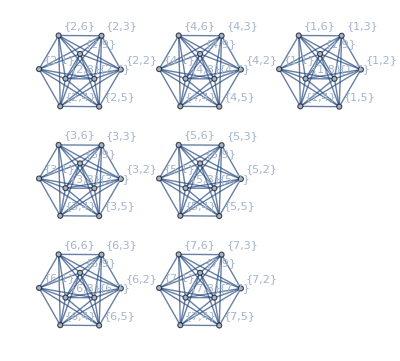

```mathematica
g=Graph[G[4,8],VertexLabels->Automatic]
```

```mathematica
{First[#],1}<->{Last[#],2}&/@Partition[Range[7],2,1,{1,1}]
```

{{1,1}<->{2,2},{2,1}<->{3,2},{3,1}<->{4,2},{4,1}<->{5,2},{5,1}<->{6,2},{6,1}<->{7,2},{7,1}<->{1,2}}

```mathematica
{First[#],3}<->{Last[#],4}&/@Partition[{1,3,5,2,7,4,6},2,1,{1,1}]
```

{{1,3}<->{3,4},{3,3}<->{5,4},{5,3}<->{2,4},{2,3}<->{7,4},{7,3}<->{4,4},{4,3}<->{6,4},{6,3}<->{1,4}}

```mathematica
{First[#],5}<->{Last[#],6}&/@Partition[{1,5,7,3,6,2,4},2,1,{1,1}]
```

{{1,5}<->{5,6},{5,5}<->{7,6},{7,5}<->{3,6},{3,5}<->{6,6},{6,5}<->{2,6},{2,5}<->{4,6},{4,5}<->{1,6}}

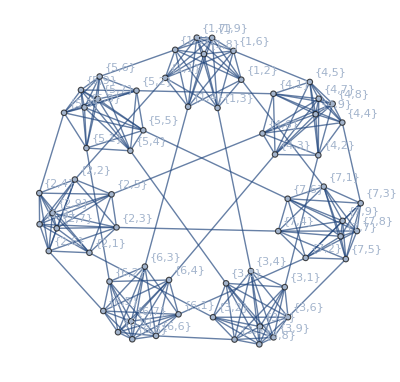

```mathematica
EdgeAdd[g,Join[%,%%,%%%]]
```

```mathematica
VertexDegree[%]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
Spectrum[%%]
```

{{Root-2.95Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.945726548275878,1},{Root-2.79Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.790292237102982,3},{Root-2.63Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.631026801505424,2},{Root-2.42Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-2.418377875757821,2},{Root-2.22Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-2.219894418526786,3},{Root-1.96Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-1.9558149132859004,1},{Root-1.60Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.6022728522004022,1},{Root-1.52Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.5230990939427331,3},{Root-1.50Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.4984738367168853,2},{-1,20},{Root-0.275Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.2746426095317641,2},{Root-0.244Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.24413307321199104,3},{Root-0.164Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.16391511063165878,1},{Root0.379Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.37931920563882626,1},{Root0.503Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.502880455004431,3},{Root0.556Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.5560737985012758,2},{Root0.937Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9369758420490687,2},{Root0.942Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9419581784639768,3},{Root0.950Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9496330226645139,1},{Root7.33Root[-10-21 #1+70 #1^2+39 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.329471482961551,2},{Root7.33Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.332580189316085,3},{Root7.34Root[-4-15 #1+64 #1^2+33 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.3387771960905,1},{8,1}}

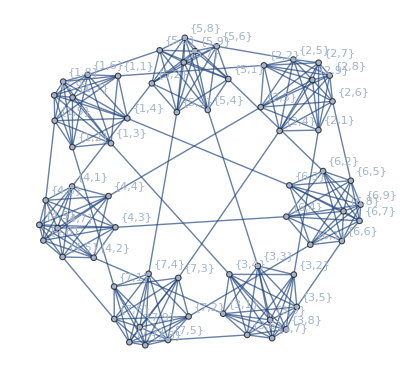

```mathematica
EdgeAdd[g,Join[
{First[#],1}<->{Last[#],2}&/@Partition[Range[7],2,1,{1,1}],
{First[#],3}<->{Last[#],4}&/@Partition[{1,3,5,7,2,4,6},2,1,{1,1}],
{First[#],5}<->{Last[#],6}&/@Partition[{1,4,7,3,6,2,5},2,1,{1,1}]
]]
```

```mathematica
VertexDegree[%]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
Spectrum[%%]
```

{{Root-2.79Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.790292237102982,6},{Root-2.22Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-2.219894418526786,6},{Root-1.52Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.5230990939427331,6},{-1,20},{Root-0.244Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.24413307321199104,6},{Root0.503Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.502880455004431,6},{Root0.942Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9419581784639768,6},{Root7.33Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.332580189316085,6},{8,1}}

```mathematica
Flatten[Table[{{i,1}<->{Mod[i-1,7,1],2},{i,3}<->{Mod[i-2,7,1],4},{i,5}<->{Mod[i-3,7,1],6}},{i,7}],1]
```

{{1,1}<->{7,2},{1,3}<->{6,4},{1,5}<->{5,6},{2,1}<->{1,2},{2,3}<->{7,4},{2,5}<->{6,6},{3,1}<->{2,2},{3,3}<->{1,4},{3,5}<->{7,6},{4,1}<->{3,2},{4,3}<->{2,4},{4,5}<->{1,6},{5,1}<->{4,2},{5,3}<->{3,4},{5,5}<->{2,6},{6,1}<->{5,2},{6,3}<->{4,4},{6,5}<->{3,6},{7,1}<->{6,2},{7,3}<->{5,4},{7,5}<->{4,6}}

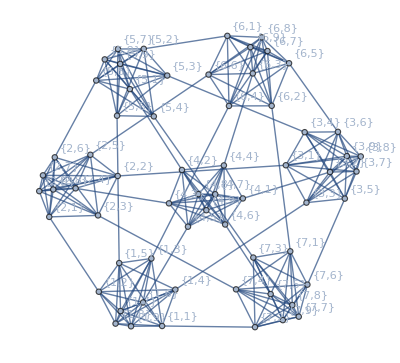

```mathematica
EdgeAdd[g,%96]
```

```mathematica
VertexDegree[%]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
Spectrum[%%]
```

{{Root-2.79Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,1]-2.790292237102982,6},{Root-2.22Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,2]-2.219894418526786,6},{Root-1.52Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,3]-1.5230990939427331,6},{-1,20},{Root-0.244Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,4]-0.24413307321199104,6},{Root0.503Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,5]0.502880455004431,6},{Root0.942Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,6]0.9419581784639768,6},{Root7.33Root[-8-19 #1+68 #1^2+37 #1^3-51 #1^4-33 #1^5-2 #1^6+#1^7&,7]7.332580189316085,6},{8,1}}

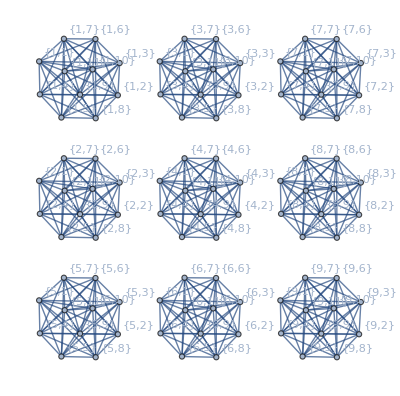

```mathematica
g=Graph[G[5,10],VertexLabels->Automatic]
```

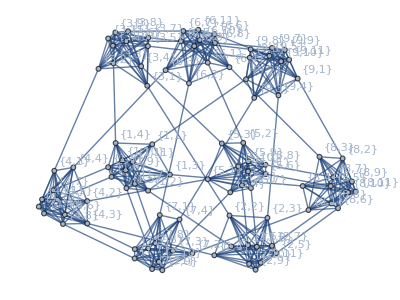

```mathematica
EdgeAdd[g,Flatten[Table[{{i,1}<->{Mod[i-1,9,1],2},{i,3}<->{Mod[i-2,9,1],4},{i,5}<->{Mod[i-3,9,1],6},{i,7}<->{Mod[i-3,9,1],8}},{i,9}],1]]
```

```mathematica
VertexDegree[%]
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
Spectrum[%%]
```

{{Root-2.90Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,1]-2.89842911796781,2},{Root-2.90Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,2]-2.8956519499770192,2},{-1-√3,8},{Root-2.47Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,3]-2.4693707245399286,2},{Root-2.42Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,4]-2.419883898654676,2},{Root-2.20Root[14-16 #1-8 #1^2+#1^3&,1]-2.19500700315004,2},{Root-2.07Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,5]-2.0662070620542234,2},{Root-1.95Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,6]-1.954593646794124,2},{Root-1.55Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,7]-1.549038172984497,2},{Root-1.41Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,8]-1.4114563475097823,2},{Root-1.40Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,9]-1.4015621037698829,2},{-1,34},{Root-0.411Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,10]-0.4114586910603308,2},{Root-0.407Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,11]-0.4068229274573423,2},{Root0.186Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,12]0.18611639723015846,2},{Root0.212Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,13]0.2117845057534735,2},{Root0.659Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,14]0.6587460638194268,2},{Root0.663Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,15]0.6633807492642345,2},{Root0.670Root[14-16 #1-8 #1^2+#1^3&,2]0.6695886221434443,2},{Root0.674Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,16]0.6737686615475472,2},{-1+√3,8},{Root0.966Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,17]0.966002130241794,2},{Root0.966Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,18]0.9660111086650132,2},{Root9.05Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,19]9.051842934447578,2},{Root9.16Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,20]9.155390092937147,2},{Root9.35Root[872-6576 #1-7716 #1^2+112468 #1^3+20232 #1^4-630216 #1^5-30141 #1^6+1533186 #1^7+351162 #1^8-1903829 #1^9-971958 #1^10+1066629 #1^11+980168 #1^12-46269 #1^13-330219 #1^14-133767 #1^15-10242 #1^16+4806 #1^17+770 #1^18-78 #1^19-12 #1^20+#1^21&,21]9.351431998863246,2},{Root9.53Root[14-16 #1-8 #1^2+#1^3&,3]9.525418381006595,2},{10,1}}

```mathematica
QuotientAdjacencyMatrix[g_Graph,s_List]:=SparseArray@Flatten[If[#1==#2,{#1,#2}->(2#3)/Length[s⟦#1⟧],{{#1,#2}->#3/Length[s⟦#1⟧],{#2,#1}->#3/Length[s⟦#2⟧]}]&@@@({First[#1],Last[#1],#2}&@@@Tally[EdgeList[g]/.Flatten[Thread/@MapIndexed[Rule[#1,First[#2]]&,s],1]]),1]
```

```mathematica
G[2,4,VertexLabels->Automatic]
```

-Graphics-

```mathematica
Join[{{#,3},{#,4},{#,5}}&/@Range[3],{{#,1}}&/@Range[3],{{#,2}}&/@Range[3]]
```

{{{1,3},{1,4},{1,5}},{{2,3},{2,4},{2,5}},{{3,3},{3,4},{3,5}},{{1,1}},{{2,1}},{{3,1}},{{1,2}},{{2,2}},{{3,2}}}

```mathematica
QuotientAdjacencyMatrix[G[2,4],Join[{{#,3},{#,4},{#,5}}&/@Range[3],{{#,1}}&/@Range[3],{{#,2}}&/@Range[3]]]//MatrixForm
```

(2 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 2 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 1
3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 3 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 1 | 0
3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0)